# Pipeline Algebra

## Embeddings + Classification

Translate the quantum circuit operations into purely matrix/vector-based operations (i.e., classical linear algebra). 💃
Represent Qubits and Registers as Vector Spaces
- Each qubit is a 2D complex vector space with computational basis ∣0⟩ = (1
0) and ∣1⟩ = (0
1).
- An 𝑛-qubit register corresponds to a tensor product space of dimension 2^𝑛.
- A full quantum state is a normalized vector in this space.
- Initialize the nodes in an equal superposition, not with different .

# Network Parameters

```mathematica
(* Parameters *)
n = 6; (* Number of qubits for |j⟩ *) (* 14 2 *)
m = 2; (* Number of qubits for |k⟩ *) (* 4 1 *)

(* Derived quantities *)
nrNodes = 2^n; (* Number of nodes *)
s = 2^m; (* Sparsity level *)
Print["Number of Nodes: ", nrNodes]

(* Initialize adjacency matrix *)
Print["Creating the Adjacency Matrix..."]
A = ConstantArray[0, {nrNodes, nrNodes}];

(* Circulant graph shifts *)
shifts = If[s <= 2,
   {1, -1},
   Join[Range[1, s/2], -Range[1, s/2]]
];

(* Build adjacency list and adjacency matrix *)
adjacencyList = Table[
   Module[{vList = Mod[i + shifts, nrNodes, 1]},
    (* Update adjacency matrix *)
    Scan[(A[[i, #]] = 1; A[[#, i]] = 1) &, vList];
    vList
    ],
   {i, 1, nrNodes}
];
(* Print["Adjacency Matrix (Sparse):", MatrixForm[A]]; 
Print["Adjacency List:", adjacencyList]; *)
Print["Finished."]

(* Calculate node degrees *)
nodeDegrees = Length /@ adjacencyList;

(* Calculate second-order node degrees using squared adjacency matrix *)
Print["Creating the A2..."]
(* A2 = A . A; 
nodeDegreesC1 = Total[A2, {2}];*)
nodeDegreesC1 = nodeDegrees^2;  (* approximation *)
Print["Finished."];

(* Calculate m_c1 = bits needed to represent max second-order degree *)
mC1 = Ceiling[Log2[Max[nodeDegreesC1]]];
Print["m_c1 (bits for 2nd order degrees): ", mC1];

(* Sparsity level for c1 *)
sC1 = 2^mC1;
Print["s_c1 (2^m_c1): ", sC1];

(* For the features *)
p = n; (* Precision level *)
P = 2^p; (* Scaling factor *)

(* Feature vector (descending from 1 - 1/P to 0) *)
features = N[Round[Subdivide[1 - 1/P, 0, nrNodes - 1], 0.0000000001]]; (* [0, 0.7, 0.3, 1];*)
featuresInt = Round[features * P];
```

Number of Nodes: 64

Creating the Adjacency Matrix...

Finished.

Creating the A2...

Finished.

m_c1 (bits for 2nd order degrees): 4

s_c1 (2^m_c1): 16

```mathematica
(*--------------------------------------- Dimensions for each register ---------------------------------------*)

swapDim = 2^5 * 2^3 * 2^m * 2^m;
fullDim = swapDim * 2^p * 2^mC1 * 2^n * 2^n * 2^n; (* dim-features * dim_Z * dim_K * dim_u1 * dim_U2 * dim_V *)

(* number of qubits: QuantumCircuit(qr_a, qr_z, qr_k, qr_u2, qr_u1, qr_l2, qr_l1, qr_c, qr_i, qr_v) *)
Print["Full dimension: ", fullDim];
Print["Swap dimension: ", swapDim];
Print["Full dim (qubits): ", Log2[fullDim]]
Print["Swap dim (qubits): ", Log2[swapDim]]
```

Full dimension: 1099511627776

Swap dimension: 4096

Full dim (qubits): 40

Swap dim (qubits): 12

# Unitary Gates

## Simple Gates

```mathematica
H = (1/Sqrt[2]) * {
  {1, 1},
  {1, -1}
};

H2 = (1/2) * {
  {1, 1, 1, 1},
  {1, -1, 1, -1},
  {1, 1, -1, -1},
  {1, -1, -1, 1}
};

H3 = (1/Sqrt[8]) * {
  {1, 1, 1, 1, 1, 1, 1, 1},
  {1, -1, 1, -1, 1, -1, 1, -1},
  {1, 1, -1, -1, 1, 1, -1, -1},
  {1, -1, -1, 1, 1, -1, -1, 1},
  {1, 1, 1, 1, -1, -1, -1, -1},
  {1, -1, 1, -1, -1, 1, -1, 1},
  {1, 1, -1, -1, -1, -1, 1, 1},
  {1, -1, -1, 1, -1, 1, 1, -1}
};

H4 = (1/4) * {
  {1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1},
  {1, -1, 1, -1, 1, -1, 1, -1, 1, -1, 1, -1, 1, -1, 1, -1},
  {1, 1, -1, -1, 1, 1, -1, -1, 1, 1, -1, -1, 1, 1, -1, -1},
  {1, -1, -1, 1, 1, -1, -1, 1, 1, -1, -1, 1, 1, -1, -1, 1},
  {1, 1, 1, 1, -1, -1, -1, -1, 1, 1, 1, 1, -1, -1, -1, -1},
  {1, -1, 1, -1, -1, 1, -1, 1, 1, -1, 1, -1, -1, 1, -1, 1},
  {1, 1, -1, -1, -1, -1, 1, 1, 1, 1, -1, -1, -1, -1, 1, 1},
  {1, -1, -1, 1, -1, 1, 1, -1, 1, -1, -1, 1, -1, 1, 1, -1},
  {1, 1, 1, 1, 1, 1, 1, 1, -1, -1, -1, -1, -1, -1, -1, -1},
  {1, -1, 1, -1, 1, -1, 1, -1, -1, 1, -1, 1, -1, 1, -1, 1},
  {1, 1, -1, -1, 1, 1, -1, -1, -1, -1, 1, 1, -1, -1, 1, 1},
  {1, -1, -1, 1, 1, -1, -1, 1, -1, 1, 1, -1, -1, 1, 1, -1},
  {1, 1, 1, 1, -1, -1, -1, -1, -1, -1, -1, -1, 1, 1, 1, 1},
  {1, -1, 1, -1, -1, 1, -1, 1, -1, 1, -1, 1, 1, -1, 1, -1},
  {1, 1, -1, -1, -1, -1, 1, 1, -1, -1, 1, 1, 1, 1, -1, -1},
  {1, -1, -1, 1, -1, 1, 1, -1, -1, 1, 1, -1, 1, -1, -1, 1}
};
```

```mathematica
(*--------------------------------------- Hadamard Matrices ---------------------------------------*)

Hl = Switch[m,
  1, H,
  2, H2,
  3, H3,
  4, H4,
  _, MessageDialog["Only m = 1 to 4 supported"]
];

(*--------------------------------------- Feature Rotation Matrix ---------------------------------------*)

Wtheta[theta_] := {
  {Cos[theta/2], -Sin[theta/2]},
  {Sin[theta/2],  Cos[theta/2]}
};

Wval[val_] := {
  {val, -Sqrt[1 - val^2]},
  {Sqrt[1 - val^2], val}
};

Print["Wtheta[0.5] =", MatrixForm[Wtheta[0.5]]];
Print["Wval[1] =", MatrixForm[Wval[0.8]]];
```

Wtheta[0.5] =(0.968912 | -0.247404
0.247404 | 0.968912)

Wval[1] =(0.8 | -0.6
0.6 | 0.8)

## OL: Equivalent Feature Rotation

Given node v and neighbor index l, it retrieves the 2x2 feature rotation matrix F_X(u=r(v,l)) to act on the 1-qubit ancilla .

```mathematica
Print["Creating FeatureRotation gate..."]
GetFeatureRotation[v_Integer, l_Integer] := Module[
  {u, featVal},

  (* Check if v and l are valid indices *)
  If[
    1 <= v <= Length[adjacencyList] && 1 <= l <= Length[adjacencyList[[v]]],
    
    u = adjacencyList[[v, l]]; (* In Mathematica, indexing starts at 1 *)
    featVal = features[[u]];
    Wval[featVal],
    (* Return identity if invalid *)
    IdentityMatrix[2]
  ]
];

MatrixForm[GetFeatureRotation[1, 1]]
MatrixForm[GetFeatureRotation[2, 1]]
MatrixForm[GetFeatureRotation[2, 2]]
Print["Finished."]
```

Creating FeatureRotation gate...

(0.96875 | -0.248039
0.248039 | 0.96875)

(0.953125 | -0.302577
0.302577 | 0.953125)

(0.9375 | -0.347985
0.347985 | 0.9375)

Finished.

## OK^-1: Equivalent Feature Rotation

Given node v and neighborhood-hop index c, it retrieves the 2x2 feature rotation matrix F_K(v) to act on the 1-qubit ancilla .

```mathematica
Print["Creating DegreeRotation gate..."]
GetDegreeRotation[v_Integer, c_Integer] := Module[
  {deg, theta},
  
  deg = Switch[c,
    1, nodeDegrees[[v]],
    2, nodeDegreesC1[[v]],
    _, Return[IdentityMatrix[2]] 
  ];

  If[deg < 1, Return[IdentityMatrix[2]]];
  theta = 2 ArcCos[1 / deg];
  Wtheta[theta]
];

MatrixForm[GetDegreeRotation[2, 1]]
MatrixForm[GetDegreeRotation[2, 2]]
Print["Finished."]
```

Creating DegreeRotation gate...

(1/4 | -(√15)/4
(√15)/4 | 1/4)

(1/16 | -(√255)/16
(√255)/16 | 1/16)

Finished.

# QMME Circuit

## c=1: Feature Embeddings for (v, l, i)

First-hop neighborhood: For each (v, l), get the 8 feature vectors (for each i, l) of dimension  = 16 (corresponding to 4 ancilla rotations).

```mathematica
Print["Creating firstHopStates..."];

firstHopStates = Reap[
  Do[
    featVec = GetFeatureRotation[v, l] . {1, 0};
    
    (* Precompute all Kronecker combinations once for each featVec *)
    vectListBase = Table[{1, 0}, {4}];
    
    Do[
      vectList = ReplacePart[vectListBase, Table[k -> featVec, {k, 1, i}]];
      combinedVec = Fold[KroneckerProduct, First[vectList], Rest[vectList]] // Flatten;
      
      Sow[<|
        "v" -> v,
        "i" -> i,
        "l" -> l,
        "u" -> adjacencyList[[v, l]],
        "featVec" -> featVec,
        "state" -> combinedVec
      |>],
      {i, 1, 4}
    ],
    {v, 1, nrNodes}, {l, 1, s}
  ]
][[2, 1]];

(* firstHopStates // TableForm *)
(* Select[firstHopStates, #v == 2 &] // TableForm *)
(* Scan[Print[Norm[#state]] &, firstHopStates] *) (* Norm = 1 for all *)
Print["Finished."]
```

Creating firstHopStates...

Finished.

## c=2: Feature Embeddings for (v, l1, l2, i) - Taking a while for real-sized Net

Second-hop neighborhood: For each (v, l1, l2), get the 16 feature vectors (for each i, l1, l2) of dimension  = 16 (corresponding to 4 ancilla rotations).

```mathematica
(* Preprocess: group firstHopStates by "v" *)
firstHopByV = GroupBy[firstHopStates, #["v"] &];

Print["Creating secondHopStates..."];
secondHopStates = Reap[
  For[v0 = 1, v0 <= nrNodes, v0++,
    For[l0 = 1, l0 <= s, l0++,
      u0 = adjacencyList[[v0, l0]];
      neighborStates = Lookup[firstHopByV, u0, {}];  (* fast! *)

      Do[
        Sow[<|
          "v" -> v0,
          "i" -> state["i"],
          "l0" -> l0,
          "u0" -> u0,
          "l1" -> state["l"],
          "u1" -> state["u"],
          "state" -> state["state"]
        |>],
        {state, neighborStates}
      ];
    ]
  ]
][[2, 1]];

(* secondHopStates // TableForm *)
(* Select[secondHopStates, #v == 3 &] // TableForm *)
(* Scan[Print[Norm[#state]] &, secondHopStates] *) (* Norm = 1 for all *)
Print["Finished."]
```

Creating secondHopStates...

Finished.

## Superposition from firstHopsStates

First-hop neighborhood: For each (v, i), get the one feature vectors of dimension  = 64 (corresponding to 5 ancilla rotations and the l register).

```mathematica
groupedByVI = GroupBy[firstHopStates, {#v, #i} &];

Print["Creating firstHopSuperposedStates..."]
firstHopSuperposedStates = KeyValueMap[
  Function[{key, states},
    Module[{c = 1, v, i, stateDim = 16, combinedState, HOnL, hadState, finalState, degRotVec},
      {v, i} = key;
      
      combinedState = Flatten[states[[All, "state"]]];  (* length = s * 16 *)

      HOnL = KroneckerProduct[Hl, IdentityMatrix[stateDim]];  (* 16s x 16s matrix *)
      hadState = HOnL . combinedState / Sqrt[s];

      degRotVec = GetDegreeRotation[v, c] . {1, 0};  (* length 2 vector *)
      finalState = Flatten[KroneckerProduct[hadState, degRotVec]];

      <|
        "c" -> c,
        "v" -> v,
        "i" -> i,
        "stateCombined" -> combinedState,
        "stateHadamardL" -> hadState,
        "degRotVec" -> degRotVec,
        "stateDegreeRotated" -> finalState
      |>
    ]
  ],
  groupedByVI
];

(* Select[firstHopSuperposedStates, #v == 2 && #i == 4 &] *)
(* Scan[Print[Norm[#stateDegreeRotated]] &, firstHopSuperposedStates]*) (* Norm = 1 for all *)
Print["Finished."]
```

Creating firstHopSuperposedStates...

Finished.

## Superposition from secondHopsStates

Second-hop neighborhood: For each (v, i), get the one feature vectors of dimension  = 128 (corresponding to 5 ancilla rotations and the l registers).

```mathematica
groupedByVI2 = GroupBy[secondHopStates, {#v, #i} &];

Print["Creating secondHopSuperposedStates..."]
secondHopSuperposedStates = KeyValueMap[
  Function[{key, states},
    Module[{c = 2, v, i, stateDim = 16, combinedState, HOnL, hadState, finalState, degRotVec},
      {v, i} = key;
      
      combinedState = Flatten[states[[All, "state"]]];  
      
      HOnL = KroneckerProduct[Hl, Hl, IdentityMatrix[stateDim]];  (* 16s^2 x 16s^2 matrix *)
      hadState = HOnL . combinedState / s;

      degRotVec = GetDegreeRotation[v, c] . {1, 0}; 
      finalState = Flatten[KroneckerProduct[hadState, degRotVec]]; (* 2 x as big as for c = 1 *)

      <|
        "c" -> c,
        "v" -> v,
        "i" -> i,
        "stateCombined" -> combinedState,
        "stateHadamardL" -> hadState,
        "degRotVec" -> degRotVec,
        "stateDegreeRotated" -> finalState
      |>
    ]
  ],
  groupedByVI2
];

(* Select[secondHopSuperposedStates, #v == 2 && #i == 4 &] *)
(* Scan[Print[Norm[#stateDegreeRotated]] &, secondHopSuperposedStates]*) (* Norm = 1 for all *)
Print["Finished."]
(*
combinedState length: 256
HOnL dimensions: {256,256}
hadState length: 256
degRotVec length: 2
finalState length: 512
Norm of finalState: 1.
*)
```

Creating secondHopSuperposedStates...

Finished.

## Feature Embeddings f_x(v,c,i)

Both neighborhoods: For each (v, c, i), get the one feature vectors of dimension  = 128 (padded and unit-length).

```mathematica
Print["Creating allSuperposedStates..."]
allSuperposedStates = Join[
  (* c = 1: pad to 2^5 * s^2 = 2^(5+2m) *)
  Map[
    Function[assoc,
      assoc ~Join~ <|
        "statePadded" -> PadRight[assoc["stateDegreeRotated"], 2^5 * s^2]
      |>
    ],
    firstHopSuperposedStates
  ],

  (* c = 2: already full size *)
  Map[
    Function[assoc,
      assoc ~Join~ <|
        "statePadded" -> assoc["stateDegreeRotated"]
      |>
    ],
    secondHopSuperposedStates
  ]
];

Map[
  Function[assoc,
    <|
      "c" -> assoc["c"],
      "i" -> assoc["i"],
      "stateLengthPadded" -> Length[assoc["statePadded"]]
    |>
  ],
  Select[allSuperposedStates, #v == 2 &]
]

(* Scan[Print[Norm[#statePadded]] &, allSuperposedStates]*) (* Norm = 1 for all *)
Print["Finished."]
```

Creating allSuperposedStates...

{<|c→1,i→1,stateLengthPadded→512|>,<|c→1,i→2,stateLengthPadded→512|>,<|c→1,i→3,stateLengthPadded→512|>,<|c→1,i→4,stateLengthPadded→512|>,<|c→2,i→1,stateLengthPadded→512|>,<|c→2,i→2,stateLengthPadded→512|>,<|c→2,i→3,stateLengthPadded→512|>,<|c→2,i→4,stateLengthPadded→512|>}

Finished.

## Feature Embeddings f_x(v)

Both neighborhoods: For each , get the one feature vectors of dimension  = 128x8=1024 (unit-length).

```mathematica
(* Group all states by v *)
vectorsByV = GroupBy[allSuperposedStates, #v &];

(* For each v, build the concatenated super-long vector by joining statePadded vectors in order *)
Print["Creating superLongVectorsByV..."]
superLongVectorsByV = Association[
  KeyValueMap[
    Function[{v, assocList},
      lookup = Association[Map[{#c, #i} -> # &, assocList]];
      
      concatenatedVector = Flatten[
        Table[
          If[KeyExistsQ[lookup, {c, i}],
            lookup[{c, i}]["statePadded"] / Sqrt[8],  (* superposition in (c,i) *)
            {}
          ],
          {c, 1, 2}, {i, 1, 4}
        ],
        Infinity
      ];
      
      v -> concatenatedVector
    ],
    vectorsByV
  ]
];

(* Norm /@ Values[superLongVectorsByV] // Print Norm = 1 for all *)
(* Print[Dimensions /@ Values[superLongVectorsByV]] *)
Print["Finished."]
```

Creating superLongVectorsByV...

Finished.

# Swap-Test Classifier

Expectation value of the product of two Pauli-Z operators acting on the ancilla qubits of the quantum classifier’s state.
It measures their correlation and captures the similarity between the test data and training data.

## Kernel Matrix on Training Data

Creating Kernel Matrix Table...

{64,64}

Creating Kernel Matrix Heatmap...

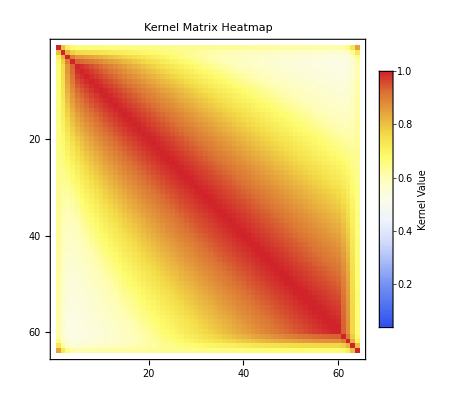

```mathematica
trainVecs = Values[superLongVectorsByV];
nPower = 1;

Print["Creating Kernel Matrix Table..."]
kernelMatrix = Table[
  (Abs[trainVecs[[i]] . trainVecs[[j]]])^(2 nPower),
  {i, Length[trainVecs]}, {j, Length[trainVecs]}
];

Dimensions[kernelMatrix] (* should be {nrNodes, nrNodes} *)

Print["Creating Kernel Matrix Heatmap..."]
Legended[
 MatrixPlot[kernelMatrix,
  ColorFunction -> "TemperatureMap",
  FrameTicks -> True,
  PlotLabel -> "Kernel Matrix Heatmap",
  ImageSize -> Large
 ],
 BarLegend[{"TemperatureMap", {Min[kernelMatrix], Max[kernelMatrix]}}, LegendLabel -> "Kernel Value"]
]
```

## Classification

```mathematica
(* Train/Test Set Details *)
thClass = 0.5;
classLabels = If[# < thClass, 0, 1] & /@ features;

wV = ConstantArray[1/nrNodes, nrNodes];
(* wV = {1/2, 1/6, 1/6, 1/6}; *)

Print["Class labels: ", classLabels];
(* Print["Features: ", features]; *)

testNode = 1; (* 1 in Mathematica. 0 in Python. *)
```

Class labels: {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
trainLabels = classLabels; (* {1, 1, 0, 0}; *)
testIsTrain = True

Print["Calculating Expectation Values..."]
expectationValsAll = If[testIsTrain,
  Table[
    Total[((-1)^trainLabels) * wV * kernelMatrix[[v]]],
    {v, Length[trainVecs]}
  ],
  
  (* if testIstrain = False, exclude self from kernel row, labels and weights *)
  Table[
    Module[{idxs = Delete[Range[Length[trainVecs]], v]},
      Total[
        ((-1)^trainLabels[[idxs]]) * wV[[idxs]] * kernelMatrix[[v, idxs]]
      ]
    ],
    {v, Length[trainVecs]}
  ]
];

Print["Calculating Predicted Labels..."]
predictedLabels = 1/2 (1 - Sign[expectationValsAll]);

results = Table[
  <|
    "Node" -> v,
    "ExpectationValue" -> expectationValsAll[[v]],
    "TrueLabel" -> trainLabels[[v]],
    "PredictedLabel" -> predictedLabels[[v]],
    "Correct" -> (predictedLabels[[v]] == trainLabels[[v]])
  |>,
  {v, Length[trainVecs]}
];

(* Print /@ results; *)
```

True

Calculating Expectation Values...

Calculating Predicted Labels...

Creating Results Bar Chart...

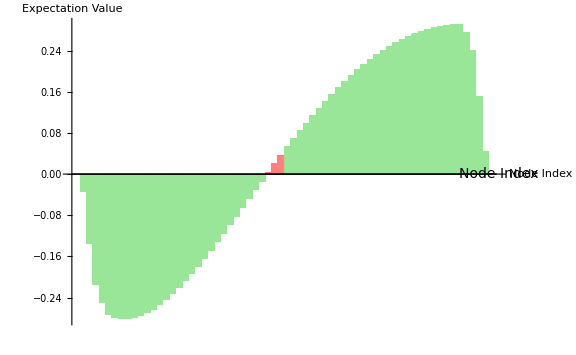

```mathematica
showLabels = True;  (* or True *)

Print["Creating Results Bar Chart..."]
BarChart[
  expectationValsAll,
  ChartStyle -> (If[#["Correct"], RGBColor[0.6, 0.9, 0.6], RGBColor[1.0, 0.5, 0.5]] & /@ results),
  (* ChartLabels -> If[
    showLabels,
    Placed[
      Map[
        Row[{
          Style["T: " <> ToString[#["TrueLabel"]], Bold],
          "\n",
          Style["P: " <> ToString[#["PredictedLabel"]], Italic]
        }] &,
        results
      ],
      Below
    ],
    None
  ], *)
  PlotLabel -> None, (* StringForm["Expectation Values per Node with Predictions (N = ``)", nrNodes],*)
  AxesLabel -> {
    Style["Node Index", 14],  (* Larger font size *)
    Style["Expectation Value", 14]
  },
  ImageSize -> Large
]
```

```mathematica
(* Compute metrics *)
trueLabels = results[[All, "TrueLabel"]];
predLabels = results[[All, "PredictedLabel"]];
posClass = 1; negClass = 0;

(* True Positives: predicted = 1 AND true = 1 *)
tp = Count[results, assoc_ /; assoc["PredictedLabel"] == posClass && assoc["TrueLabel"] == posClass];
(* False Positives: predicted = 1 AND true = 0 *)
fp = Count[results, assoc_ /; assoc["PredictedLabel"] == posClass && assoc["TrueLabel"] == negClass];
(* False Negatives: predicted = 0 AND true = 1 *)
fn = Count[results, assoc_ /; assoc["PredictedLabel"] == negClass && assoc["TrueLabel"] == posClass];

accuracy = N[Count[results[[All, "Correct"]], True]/Length[results]]; (* correct / all *)
precision = If[tp + fp == 0, 0, N[tp/(tp + fp)]]; (*tp / all predicted positives*)
recall = If[tp + fn == 0, 0, N[tp/(tp + fn)]]; (* tp / all real positives *)
f1 = If[precision + recall == 0, 0, 2*precision*recall/(precision + recall)];

(* Metrics table *)
metricsTable = Grid[
  {{"Metric", "Value"},
   {"Accuracy", accuracy},
   {"Precision", precision},
   {"Recall", recall},
   {"F1 Score", f1}},
  Frame -> All
];

metricsTable
```

Metric | Value
Accuracy | 0.953125
Precision | 1.
Recall | 0.90625
F1 Score | 0.95082